# SU(3) in 1+2D (A_μ^a=f(t,x))

```mathematica
coord={t,x,y,z};
n=4;(*# of spacetime dimensions*)
```

```mathematica
(*Minkowski*)
```

```mathematica
gdd={{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
gUU={{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
(*Christoffel  symbols*)
```

```mathematica
ΓUdd=Table[1/2 Sum[gUU[[i]][[l]](D[gdd[[l]][[k]],coord[[j]]]+D[gdd[[l]][[j]],coord[[k]]]-D[ gdd[[j]][[k]],coord[[l]]]),{l,1,n}],{i,1,n},{j,1,n},{k,1,n}];
```

```mathematica
(*Gellmann matrices*)
```

```mathematica
nn=3;(* for SU(N),nn=N*)
λ1={SparseArray[{{1,2}->1,{2,1}->1,{3,3}->0}]};
λ2={SparseArray[{{1,2}->-I,{2,1}->I,{3,3}->0}]};
λ3={SparseArray[{{1,1}->1,{2,2}->-1,{3,3}->0}]};
λ4={SparseArray[{{1,3}->1,{3,1}->1,{3,3}->0}]};
λ5={SparseArray[{{1,3}->-I,{3,1}->I,{3,3}->0}]};λ6={SparseArray[{{2,3}->1,{3,2}->1,{3,3}->0}]};
λ7={SparseArray[{{2,3}->-I,{3,2}->I,{3,3}->0}]};
λ8={1/(√3)SparseArray[{{1,1}->1,{2,2}->1,{3,3}->-2}]};
basis=Join[λ1,λ2,λ3,λ4,λ5,λ6,λ7,λ8];
mat=Normal[basis]
```

{{{0,1,0},{1,0,0},{0,0,0}},{{0,-ⅈ,0},{ⅈ,0,0},{0,0,0}},{{1,0,0},{0,-1,0},{0,0,0}},{{0,0,1},{0,0,0},{1,0,0}},{{0,0,-ⅈ},{0,0,0},{ⅈ,0,0}},{{0,0,0},{0,0,1},{0,1,0}},{{0,0,0},{0,0,-ⅈ},{0,ⅈ,0}},{{1/(√3),0,0},{0,1/(√3),0},{0,0,-2/(√3)}}}

```mathematica
(*Structure constants for SU(3)*)
```

```mathematica
fabc=Table[-I/4 Tr[(mat[[i]].mat[[j]]-mat[[j]].mat[[i]]).ConjugateTranspose[mat[[k]]]],{i,1,8},{j,1,8},{k,1,8}];
```

```mathematica
m=8;(*# of internal indices (SU(3))*)
```

```mathematica
(*Gauge field A with 'a' as internal index and d as spacetime index= Aad*)
```

```mathematica
(*All the combinations in selecting 3 numbers from 1 to 8 numbers*)
```

```mathematica
s=Table[{a,b,c},{a,1,8},{b,1,8},{c,1,8}];
```

```mathematica
s1=Flatten[s,2];
```

```mathematica
(*Making the set with equal numbers to zero*)
```

```mathematica
s2=Table[If[s1[[i]][[1]]==s1[[i]][[2]]||s1[[i]][[1]]==s1[[i]][[3]],0,If[s1[[i]][[2]]==s1[[i]][[3]],0, s1[[i]]]],{i,1,Length[s1]}];
```

```mathematica
s3=DeleteCases[s2,0];
```

```mathematica
(*Making the elements in set in ascending order*)
```

```mathematica
s4=Table[Sort[s3[[i]]],{i,1,Length[s3]}];
```

```mathematica
(*Removing the sets with same elements*)
```

```mathematica
s5=DeleteDuplicates[s4]
```

{{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,2,7},{1,2,8},{1,3,4},{1,3,5},{1,3,6},{1,3,7},{1,3,8},{1,4,5},{1,4,6},{1,4,7},{1,4,8},{1,5,6},{1,5,7},{1,5,8},{1,6,7},{1,6,8},{1,7,8},{2,3,4},{2,3,5},{2,3,6},{2,3,7},{2,3,8},{2,4,5},{2,4,6},{2,4,7},{2,4,8},{2,5,6},{2,5,7},{2,5,8},{2,6,7},{2,6,8},{2,7,8},{3,4,5},{3,4,6},{3,4,7},{3,4,8},{3,5,6},{3,5,7},{3,5,8},{3,6,7},{3,6,8},{3,7,8},{4,5,6},{4,5,7},{4,5,8},{4,6,7},{4,6,8},{4,7,8},{5,6,7},{5,6,8},{5,7,8},{6,7,8}}

```mathematica
(*These are total 56 unique combinations*)
```

```mathematica
(*Ap=set containing nonzero elements, Ag=the guage field for a single combination*)
```

```mathematica
Ap={{0,0,ϕ,0},{0,ψ,0,0},{ξ,0,0,m3 ξ}};Ag=ConstantArray[0,{8,4}];
```

```mathematica
(*Agg=Matric containing the gauge field ansatzs for all combinations*)
```

```mathematica
Agg=ConstantArray[0,{56,8,4}];
```

```mathematica
For[k=1,k<57,k++,Ag=ConstantArray[0,{8,4}];For[i=1,i<9,i++,For[j=1,j<4,j++,If[s5[[k]][[j]]==i,Ag[[i]]=Ap[[j]];Break[],Continue[]]]];Agg[[k]]=Ag]
```

```mathematica
(*In Hamiton gauge, Subscript[A, 0]^a=0*)
```

```mathematica
Aad=
```

```mathematica
Aad={{0,U[t],0,0},{0,0,U[t],0},{0,0,0,V[t]},{0,U[t],0,0},{0,0,U[t],0},{0,U[t],0,0},{0,0,U[t],0},{0,0,0,V[t]}}
```

{{0,U[t],0,0},{0,0,U[t],0},{0,0,0,V[t]},{0,U[t],0,0},{0,0,U[t],0},{0,U[t],0,0},{0,0,U[t],0},{0,0,0,V[t]}}

```mathematica
Aad//MatrixForm
```

(0 | U[t] | 0 | 0
0 | 0 | U[t] | 0
0 | 0 | 0 | V[t]
0 | U[t] | 0 | 0
0 | 0 | U[t] | 0
0 | U[t] | 0 | 0
0 | 0 | U[t] | 0
0 | 0 | 0 | V[t])

```mathematica
Clear[g]
```

```mathematica
(*Field strength tensor(Subscript[F, μν])*)
```

```mathematica
Fadd=Table[D[Aad[[a]][[j]],coord[[i]]]- D[Aad[[a]][[i]],coord[[j]]] +g Sum[fabc[[a]][[b]][[c]] Aad[[b]][[i]]Aad[[c]][[j]],{b,1,m},{c,1,m}],{a,1,m},{i,1,n},{j,1,n}];
```

```mathematica
(*F^μν*)
```

```mathematica
FaUU=Table[Sum[gUU[[i]][[k]]gUU[[j]][[l]]Fadd[[a]][[k]][[l]],{k,1,n},{l,1,n}],{a,1,m},{i,1,n},{j,1,n}];
```

```mathematica
(*∇_μ F^μν*)
```

```mathematica
CovDFaUU=Table[Sum[D[FaUU[[a]][[k]][[j]],coord[[k]]] +Sum[ ΓUdd[[k]][[k]][[l]] FaUU[[a]][[l]][[j]] + ΓUdd[[j]][[k]][[l]]FaUU[[a]][[k]][[l]],{l,1,n}] ,{k,1,n}],{a,1,m},{j,1,n}];
```

```mathematica
(*g Subscript[f, abc] Subscript[A, μ]^b F^cμν*)
```

```mathematica
NonaU=Table[Sum[g fabc[[a]][[b]][[c]] Aad[[b]][[i]] FaUU[[c]][[i]][[j]],{b,1,m},{c,1,m},{i,1,n}],{a,1,m},{j,1,n}];
```

```mathematica
(*∇_μ F^μν+g Subscript[f, abc] Subscript[A, μ]^b F^cμν*)
```

```mathematica
YMeq=CovDFaUU+NonaU;
```

```mathematica
YMeq[[1]]
```

{0,-3/2 g^2 U[t]^3-g^2 U[t] V[t]^2-U''[t],0,1/2 g^2 U[t] (-1/2 U[t] V[t]-1/2 √3 U[t] V[t])+1/2 g^2 U[t] (1/2 U[t] V[t]-1/2 √3 U[t] V[t])-1/2 g^2 U[t] (-1/2 U[t] V[t]+1/2 √3 U[t] V[t])-1/2 g^2 U[t] (1/2 U[t] V[t]+1/2 √3 U[t] V[t])}

```mathematica
YMeq[[2]]
```

{0,0,-3/2 g^2 U[t]^3-g^2 U[t] V[t]^2-U''[t],0}

```mathematica
YMeq[[3]]
```

{0,3/2 g^2 U[t]^3,0,-2 g^2 U[t]^2 V[t]+1/2 g^2 U[t] (-1/2 U[t] V[t]-1/2 √3 U[t] V[t])-1/2 g^2 U[t] (1/2 U[t] V[t]-1/2 √3 U[t] V[t])+1/2 g^2 U[t] (-1/2 U[t] V[t]+1/2 √3 U[t] V[t])-1/2 g^2 U[t] (1/2 U[t] V[t]+1/2 √3 U[t] V[t])-V''[t]}

```mathematica
Collect[YMeq[[1]][[2]]//Simplify,g]
```

1/4 g^2 (3 A_(2,2)[t,x] A_(4,2)[t,x] A_(5,1)[t,x]-3 A_(2,2)[t,x] A_(4,1)[t,x] A_(5,2)[t,x]-3 A_(3,2)[t,x] A_(4,2)[t,x] A_(6,1)[t,x]+3 A_(3,2)[t,x] A_(4,1)[t,x] A_(6,2)[t,x]-3 A_(3,2)[t,x] A_(5,2)[t,x] A_(7,1)[t,x]-3 A_(2,2)[t,x] A_(6,2)[t,x] A_(7,1)[t,x]+3 A_(3,2)[t,x] A_(5,1)[t,x] A_(7,2)[t,x]+3 A_(2,2)[t,x] A_(6,1)[t,x] A_(7,2)[t,x]+A_(1,2)[t,x] (4 A_(2,1)[t,x] A_(2,2)[t,x]+4 A_(3,1)[t,x] A_(3,2)[t,x]+A_(4,1)[t,x] A_(4,2)[t,x]+A_(5,1)[t,x] A_(5,2)[t,x]+A_(6,1)[t,x] A_(6,2)[t,x]+A_(7,1)[t,x] A_(7,2)[t,x])-A_(1,1)[t,x] (4 (A_(2,2)[t,x])^2+4 (A_(3,2)[t,x])^2+(A_(4,2)[t,x])^2+(A_(5,2)[t,x])^2+(A_(6,2)[t,x])^2+(A_(7,2)[t,x])^2)-2 √3 A_(4,2)[t,x] A_(6,2)[t,x] A_(8,1)[t,x]-2 √3 A_(5,2)[t,x] A_(7,2)[t,x] A_(8,1)[t,x]+√3 A_(4,2)[t,x] A_(6,1)[t,x] A_(8,2)[t,x]+√3 A_(4,1)[t,x] A_(6,2)[t,x] A_(8,2)[t,x]+√3 A_(5,2)[t,x] A_(7,1)[t,x] A_(8,2)[t,x]+√3 A_(5,1)[t,x] A_(7,2)[t,x] A_(8,2)[t,x])+1/4 g (4 A_(3,2)[t,x] (A_(2,2))^(0,1)[t,x]-4 A_(2,2)[t,x] (A_(3,2))^(0,1)[t,x]+2 A_(7,2)[t,x] (A_(4,2))^(0,1)[t,x]-2 A_(6,2)[t,x] (A_(5,2))^(0,1)[t,x]+2 A_(5,2)[t,x] (A_(6,2))^(0,1)[t,x]-2 A_(4,2)[t,x] (A_(7,2))^(0,1)[t,x])-(A_(1,1))^(2,0)[t,x]

```mathematica
Collect[YMeq[[1]][[3]]//Simplify,g]
```

1/4 g^2 (-3 A_(2,1)[t,x] A_(4,2)[t,x] A_(5,1)[t,x]+3 A_(2,1)[t,x] A_(4,1)[t,x] A_(5,2)[t,x]+3 A_(3,1)[t,x] A_(4,2)[t,x] A_(6,1)[t,x]-3 A_(3,1)[t,x] A_(4,1)[t,x] A_(6,2)[t,x]+3 A_(3,1)[t,x] A_(5,2)[t,x] A_(7,1)[t,x]+3 A_(2,1)[t,x] A_(6,2)[t,x] A_(7,1)[t,x]-A_(1,2)[t,x] (4 (A_(2,1)[t,x])^2+4 (A_(3,1)[t,x])^2+(A_(4,1)[t,x])^2+(A_(5,1)[t,x])^2+(A_(6,1)[t,x])^2+(A_(7,1)[t,x])^2)-3 A_(3,1)[t,x] A_(5,1)[t,x] A_(7,2)[t,x]-3 A_(2,1)[t,x] A_(6,1)[t,x] A_(7,2)[t,x]+A_(1,1)[t,x] (4 A_(2,1)[t,x] A_(2,2)[t,x]+4 A_(3,1)[t,x] A_(3,2)[t,x]+A_(4,1)[t,x] A_(4,2)[t,x]+A_(5,1)[t,x] A_(5,2)[t,x]+A_(6,1)[t,x] A_(6,2)[t,x]+A_(7,1)[t,x] A_(7,2)[t,x])+√3 A_(4,2)[t,x] A_(6,1)[t,x] A_(8,1)[t,x]+√3 A_(4,1)[t,x] A_(6,2)[t,x] A_(8,1)[t,x]+√3 A_(5,2)[t,x] A_(7,1)[t,x] A_(8,1)[t,x]+√3 A_(5,1)[t,x] A_(7,2)[t,x] A_(8,1)[t,x]-2 √3 A_(4,1)[t,x] A_(6,1)[t,x] A_(8,2)[t,x]-2 √3 A_(5,1)[t,x] A_(7,1)[t,x] A_(8,2)[t,x])+1/4 g (4 A_(3,2)[t,x] (A_(2,1))^(0,1)[t,x]-8 A_(3,1)[t,x] (A_(2,2))^(0,1)[t,x]-4 A_(2,2)[t,x] (A_(3,1))^(0,1)[t,x]+8 A_(2,1)[t,x] (A_(3,2))^(0,1)[t,x]+2 A_(7,2)[t,x] (A_(4,1))^(0,1)[t,x]-4 A_(7,1)[t,x] (A_(4,2))^(0,1)[t,x]-2 A_(6,2)[t,x] (A_(5,1))^(0,1)[t,x]+4 A_(6,1)[t,x] (A_(5,2))^(0,1)[t,x]+2 A_(5,2)[t,x] (A_(6,1))^(0,1)[t,x]-4 A_(5,1)[t,x] (A_(6,2))^(0,1)[t,x]-2 A_(4,2)[t,x] (A_(7,1))^(0,1)[t,x]+4 A_(4,1)[t,x] (A_(7,2))^(0,1)[t,x])+1/4 (4 (A_(1,2))^(0,2)[t,x]-4 (A_(1,2))^(2,0)[t,x])

```mathematica
(*Discretization*)
```

```mathematica
h=0.1;nn=IntegerPart[10/h];x0=0;nn
```

100

```mathematica
(*i for equations, j for points*)
```

```mathematica
Amat[t_]=Flatten[Table[Subscript[AA, a,i,j][t],{a,1,m},{i,1,2},{j,1,nn}]];
```

```mathematica
(*getting time derivative terms on one side *)
```

```mathematica
ss=Flatten[Table[Derivative[2,0][Subscript[A, a,i]][t,x]/.Solve[YMeq[[a]][[i+1]]==0,Derivative[2,0][Subscript[A, a,i]][t,x]],{a,1,m},{i,1,2}]]
```

{1/4 (4 g^2 A_(1,2)[t,x] A_(2,1)[t,x] A_(2,2)[t,x]-4 g^2 A_(1,1)[t,x] (A_(2,2)[t,x])^2+4 g^2 A_(1,2)[t,x] A_(3,1)[t,x] A_(3,2)[t,x]-4 g^2 A_(1,1)[t,x] (A_(3,2)[t,x])^2+g^2 A_(1,2)[t,x] A_(4,1)[t,x] A_(4,2)[t,x]-g^2 A_(1,1)[t,x] (A_(4,2)[t,x])^2+3 g^2 A_(2,2)[t,x] A_(4,2)[t,x] A_(5,1)[t,x]-3 g^2 A_(2,2)[t,x] A_(4,1)[t,x] A_(5,2)[t,x]+23+√3 g^2 A_(4,1)[t,x] A_(6,2)[t,x] A_(8,2)[t,x]+√3 g^2 A_(5,2)[t,x] A_(7,1)[t,x] A_(8,2)[t,x]+√3 g^2 A_(5,1)[t,x] A_(7,2)[t,x] A_(8,2)[t,x]+4 g A_(3,2)[t,x] (A_(2,2))^(0,1)[t,x]-4 g A_(2,2)[t,x] (A_(3,2))^(0,1)[t,x]+2 g A_(7,2)[t,x] (A_(4,2))^(0,1)[t,x]-2 g A_(6,2)[t,x] (A_(5,2))^(0,1)[t,x]+2 g A_(5,2)[t,x] (A_(6,2))^(0,1)[t,x]-2 g A_(4,2)[t,x] (A_(7,2))^(0,1)[t,x]),1/4 (1),12,-1/4 √3 g (1),1/4 (-√3 g^2 A_(3,2)[t,x] (A_(4,1)[t,x])^2+51+4 A_1^(0,2)[t,x])}
 |  |  |  |

```mathematica
(*Replacing spatial derivatives using finite difference methods (O(h^2))*)
```

```mathematica
ssf=ss/.{Subscript[A, a_,i_][t,x]->Subscript[AA, a,i,j][t],Derivative[0,1][Subscript[A, a_,i_]][t,x]->1/(2h)(Subscript[AA, a,i,j+1][t]-Subscript[AA, a,i,j-1][t]),Derivative[0,2][Subscript[A, a_,i_]][t,x]->1/h^2(Subscript[AA, a,i,j-1][t]-2 Subscript[AA, a,i,j][t]+Subscript[AA, a,i,j+1][t])}
```

{1/4 (4 g^2 AA_(1,2,j)[t] AA_(2,1,j)[t] AA_(2,2,j)[t]-4 g^2 AA_(1,1,j)[t] (AA_(2,2,j)[t])^2+20. g (-AA_(2,2,-1+j)[t]+AA_(2,2,1+j)[t]) AA_(3,2,j)[t]+4 g^2 AA_(1,2,j)[t] AA_(3,1,j)[t] AA_(3,2,j)[t]-4 g^2 AA_(1,1,j)[t] (AA_(3,2,j)[t])^2-20. g AA_(2,2,j)[t] (-AA_(3,2,-1+j)[t]+AA_(3,2,1+j)[t])+34+√3 g^2 AA_(4,2,j)[t] AA_(6,1,j)[t] AA_(8,2,j)[t]+√3 g^2 AA_(4,1,j)[t] AA_(6,2,j)[t] AA_(8,2,j)[t]+√3 g^2 AA_(5,2,j)[t] AA_(7,1,j)[t] AA_(8,2,j)[t]+√3 g^2 AA_(5,1,j)[t] AA_(7,2,j)[t] AA_(8,2,j)[t]),1/4 (1),1/4 (-4 g^2 1^2 AA_(2,1,j)[t]+46),1/4 (1),9,1/4 (1),-1/4 √3 g (-g AA_(3,2,j)[t] AA_(4,1,j)[t] AA_(4,2,j)[t]+47),1/4 (-√3 g^2 AA_(3,2,j)[t] (AA_(4,1,j)[t])^2+51+400. (AA_(8,2,-1+j)[t]-2 AA_(8,2,j)[t]+AA_(8,2,1+j)[t]))}
 |  |  |  |

```mathematica
ssf[[1]]
```

1/4 (4 g^2 AA_(1,2,j)[t] AA_(2,1,j)[t] AA_(2,2,j)[t]-4 g^2 AA_(1,1,j)[t] (AA_(2,2,j)[t])^2+20. g (-AA_(2,2,-1+j)[t]+AA_(2,2,1+j)[t]) AA_(3,2,j)[t]+4 g^2 AA_(1,2,j)[t] AA_(3,1,j)[t] AA_(3,2,j)[t]-4 g^2 AA_(1,1,j)[t] (AA_(3,2,j)[t])^2-20. g AA_(2,2,j)[t] (-AA_(3,2,-1+j)[t]+AA_(3,2,1+j)[t])+g^2 AA_(1,2,j)[t] AA_(4,1,j)[t] AA_(4,2,j)[t]-g^2 AA_(1,1,j)[t] (AA_(4,2,j)[t])^2+3 g^2 AA_(2,2,j)[t] AA_(4,2,j)[t] AA_(5,1,j)[t]-3 g^2 AA_(2,2,j)[t] AA_(4,1,j)[t] AA_(5,2,j)[t]+g^2 AA_(1,2,j)[t] AA_(5,1,j)[t] AA_(5,2,j)[t]-g^2 AA_(1,1,j)[t] (AA_(5,2,j)[t])^2-3 g^2 AA_(3,2,j)[t] AA_(4,2,j)[t] AA_(6,1,j)[t]+3 g^2 AA_(3,2,j)[t] AA_(4,1,j)[t] AA_(6,2,j)[t]-10. g (-AA_(5,2,-1+j)[t]+AA_(5,2,1+j)[t]) AA_(6,2,j)[t]+g^2 AA_(1,2,j)[t] AA_(6,1,j)[t] AA_(6,2,j)[t]-g^2 AA_(1,1,j)[t] (AA_(6,2,j)[t])^2+10. g AA_(5,2,j)[t] (-AA_(6,2,-1+j)[t]+AA_(6,2,1+j)[t])-3 g^2 AA_(3,2,j)[t] AA_(5,2,j)[t] AA_(7,1,j)[t]-3 g^2 AA_(2,2,j)[t] AA_(6,2,j)[t] AA_(7,1,j)[t]+10. g (-AA_(4,2,-1+j)[t]+AA_(4,2,1+j)[t]) AA_(7,2,j)[t]+3 g^2 AA_(3,2,j)[t] AA_(5,1,j)[t] AA_(7,2,j)[t]+3 g^2 AA_(2,2,j)[t] AA_(6,1,j)[t] AA_(7,2,j)[t]+g^2 AA_(1,2,j)[t] AA_(7,1,j)[t] AA_(7,2,j)[t]-g^2 AA_(1,1,j)[t] (AA_(7,2,j)[t])^2-10. g AA_(4,2,j)[t] (-AA_(7,2,-1+j)[t]+AA_(7,2,1+j)[t])-2 √3 g^2 AA_(4,2,j)[t] AA_(6,2,j)[t] AA_(8,1,j)[t]-2 √3 g^2 AA_(5,2,j)[t] AA_(7,2,j)[t] AA_(8,1,j)[t]+√3 g^2 AA_(4,2,j)[t] AA_(6,1,j)[t] AA_(8,2,j)[t]+√3 g^2 AA_(4,1,j)[t] AA_(6,2,j)[t] AA_(8,2,j)[t]+√3 g^2 AA_(5,2,j)[t] AA_(7,1,j)[t] AA_(8,2,j)[t]+√3 g^2 AA_(5,1,j)[t] AA_(7,2,j)[t] AA_(8,2,j)[t])

```mathematica
Table[ssf[[1]],{j,1,nn-1}]
```

{1/4 (4 g^2 AA_(1,2,1)[t] AA_(2,1,1)[t] AA_(2,2,1)[t]-4 g^2 AA_(1,1,1)[t] (AA_(2,2,1)[t])^2+20. g (-AA_(2,2,0)[t]+AA_(2,2,2)[t]) AA_(3,2,1)[t]+4 g^2 AA_(1,2,1)[t] AA_(3,1,1)[t] AA_(3,2,1)[t]-4 g^2 AA_(1,1,1)[t] (AA_(3,2,1)[t])^2-20. g AA_(2,2,1)[t] (-AA_(3,2,0)[t]+AA_(3,2,2)[t])+g^2 AA_(1,2,1)[t] AA_(4,1,1)[t] AA_(4,2,1)[t]-g^2 AA_(1,1,1)[t] (AA_(4,2,1)[t])^2+31+√3 g^2 AA_(4,2,1)[t] AA_(6,1,1)[t] AA_(8,2,1)[t]+√3 g^2 AA_(4,1,1)[t] AA_(6,2,1)[t] AA_(8,2,1)[t]+√3 g^2 AA_(5,2,1)[t] AA_(7,1,1)[t] AA_(8,2,1)[t]+√3 g^2 AA_(5,1,1)[t] AA_(7,2,1)[t] AA_(8,2,1)[t]),1/4 (1),95,1/4 (1),1/4 (4 g^2 AA_(1,2,99)[t] AA_(2,1,99)[t] AA_(2,2,99)[t]-4 g^2 AA_(1,1,99)[t] (AA_(2,2,99)[t])^2+42+√3 g^2 AA_(5,2,99)[t] AA_(7,1,99)[t] AA_(8,2,99)[t]+√3 g^2 AA_(5,1,99)[t] AA_(7,2,99)[t] AA_(8,2,99)[t])}
 |  |  |  |

```mathematica
eq=Flatten[Table[Join[{0.01},Table[ssf[[k]],{j,2,nn-1}],{0.01}],{k,1,2m}]];
```

```mathematica
Length[%]
```

1600

```mathematica
(*defining equations*)
```

```mathematica
g=0.5;
```

```mathematica
eqns=Thread[D[Amat[t],t,t]==eq];
```

```mathematica
ics=Thread[Join[Amat[0],Amat'[0]]==Join[Table[0.02,{i,1,2m*nn}],Table[0,{i,1,2m*nn}]]];
```

```mathematica
Molsol=NDSolve[{eqns,ics},Amat[t],{t,0,10},MaxStepSize->0.1]
```

{{AA_(1,1,1)[t]→InterpolatingFunction[…][t],AA_(1,1,2)[t]→InterpolatingFunction[…][t],AA_(1,1,3)[t]→InterpolatingFunction[…][t],AA_(1,1,4)[t]→InterpolatingFunction[…][t],AA_(1,1,5)[t]→InterpolatingFunction[…][t],AA_(1,1,6)[t]→InterpolatingFunction[…][t],AA_(1,1,7)[t]→InterpolatingFunction[…][t],AA_(1,1,8)[t]→InterpolatingFunction[…][t],1584,AA_(8,2,93)[t]→InterpolatingFunction[…][t],AA_(8,2,94)[t]→InterpolatingFunction[…][t],AA_(8,2,95)[t]→InterpolatingFunction[…][t],AA_(8,2,96)[t]→InterpolatingFunction[…][t],AA_(8,2,97)[t]→InterpolatingFunction[…][t],AA_(8,2,98)[t]→InterpolatingFunction[…][t],AA_(8,2,99)[t]→InterpolatingFunction[…][t],AA_(8,2,100)[t]→InterpolatingFunction[…][t]}}
 |  |  |  |

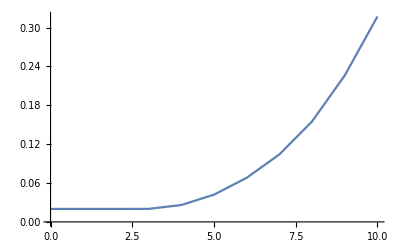

```mathematica
ListPlot[Evaluate[Table[{t,First[Subscript[AA, 1,2,30][t]/. Molsol]},{t,0,10}]],Joined->True](*for plotting at certain z without generating interpolating function*)
```

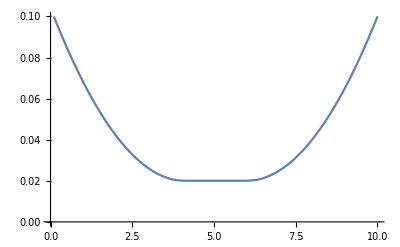

```mathematica
ListPlot[Evaluate[Table[{i h,First[Subscript[AA, 1,2,i][t]/. Molsol]/.t->4},{i,1,nn}]],Joined->True](*for plotting at certain t without generating interpolating function*)
```

```mathematica
ParametricPlot3D[Evaluate[Table[{i h,t,First[Subscript[AA, 1,2,i][t]/. Molsol]},{i,1,nn}]],{t,0,10},PlotRange->All,AxesLabel->{"x","t","AA"}]
```

-Graphics3D-

```mathematica
AA11=Interpolation[Flatten[Table[{{t,i h},First[Subscript[AA, 1,1,i][t]/. Molsol]},{i,1,nn},{t,0,10}],1],InterpolationOrder->1];
```

```mathematica
AA12=Interpolation[Flatten[Table[{{t,i h},First[Subscript[AA, 1,2,i][t]/. Molsol]},{i,1,nn},{t,0,10}],1],InterpolationOrder->1];
```

```mathematica
Plot3D[{AA11[t,x],AA12[t,x]},{t,0,10},{x,0.1,10.}]
```

-Graphics3D-

## Hamiltonian Procedure

```mathematica
(*Momentum*)
```

```mathematica
Pmat[t_]=Flatten[Table[Subscript[PP,a,i,j][t],{a,1,m},{i,1,2},{j,1,nn}]];
```

```mathematica
(*defining equations*)
```

```mathematica
eqns1=Join[Thread[D[Amat[t],t]==Pmat[t]],Thread[D[Pmat[t],t]==eq]];
```

```mathematica
ics=Thread[Join[Amat[0],Pmat[0]]==Join[Table[0.02,{i,1,2m*nn}],Table[0,{i,1,2m*nn}]]];
```

```mathematica
Val={0.2,0,0.1,0.1,0,0.1,0.2,0,0.1,0.1,0,0.1,0.2,0,0.1,0.1,0,0,0,0.1,0,0.1,0,0,0,0.1,0,0.1,0,0,0,0.1}
```

{0.2,0,0.1,0.1,0,0.1,0.2,0,0.1,0.1,0,0.1,0.2,0,0.1,0.1,0,0,0,0.1,0,0.1,0,0,0,0.1,0,0.1,0,0,0,0.1}

```mathematica
icv=Flatten[Table[Table[Val[[j]],{i,1,nn}],{j,1,32}]];
```

```mathematica
ics1=Thread[Join[Amat[0],Pmat[0]]==icv];
```

```mathematica
HMsol=NDSolve[{eqns1,ics1},Join[Amat[t],Pmat[t]],{t,0,20},MaxStepSize->0.1]
```

{{AA_(1,1,1)[t]→InterpolatingFunction[…][t],AA_(1,1,2)[t]→InterpolatingFunction[…][t],AA_(1,1,3)[t]→InterpolatingFunction[…][t],AA_(1,1,4)[t]→InterpolatingFunction[…][t],AA_(1,1,5)[t]→InterpolatingFunction[…][t],AA_(1,1,6)[t]→InterpolatingFunction[…][t],AA_(1,1,7)[t]→InterpolatingFunction[…][t],AA_(1,1,8)[t]→InterpolatingFunction[…][t],3184,PP_(8,2,93)[t]→InterpolatingFunction[…][t],PP_(8,2,94)[t]→InterpolatingFunction[…][t],PP_(8,2,95)[t]→InterpolatingFunction[…][t],PP_(8,2,96)[t]→InterpolatingFunction[…][t],PP_(8,2,97)[t]→InterpolatingFunction[…][t],PP_(8,2,98)[t]→InterpolatingFunction[…][t],PP_(8,2,99)[t]→InterpolatingFunction[…][t],PP_(8,2,100)[t]→InterpolatingFunction[…][t]}}
 |  |  |  |

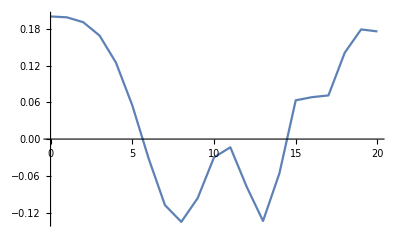

```mathematica
ListPlot[Evaluate[Table[{t,First[Subscript[AA, 1,1,6][t]/. HMsol]},{t,0,20}]],Joined->True](*for plotting at certain z without generating interpolating function*)
```

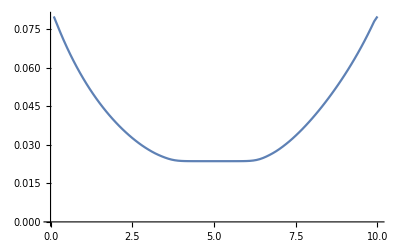

```mathematica
ListPlot[Evaluate[Table[{i h,First[Subscript[AA, 1,2,i][t]/. HMsol]/.t->4},{i,1,nn}]],Joined->True](*for plotting at certain t without generating interpolating function*)
```

```mathematica
ParametricPlot3D[Evaluate[Table[{i h,t,First[Subscript[AA, 4,1,i][t]/. HMsol]},{i,1,nn}]],{t,0,20},PlotRange->All,AxesLabel->{"x","t","AA"}]
```

-Graphics3D-

```mathematica
sol=NDSolve[{eqns1,ics1},vars,{t,0,10},Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->2,"PositionVariables"->Amat[t]},StartingStepSize->0.2]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

NDSolve::nlnum1: The function value {0.01,Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],1.618791259942552`15.954589770191005*^897861325806500,3.491748876619825`15.954589770191005*^513924241803802,-4.756002629650564`15.954589770191005*^289079914590293,9.48144998451316`15.954589770191005*^158953093310009,«1590»} is not a list of numbers with dimensions {1600} when the arguments are {7.8,0.5042,1.441962362581392`15.954589770191005*^729497019469700,2.29199765926918`15.954589770191005*^738349419378847,2.979091969817614`15.954589770191005*^766765912175207,1.170320171402483`15.954589770191005*^670892660492178,2.082792083939166`15.954589770191005*^454632174943817,-2.172425422514286`15.954589770191005*^299287108602166,-2.09662794577798`15.954589770191005*^171308080601267,3.180516091454775`15.954589770191005*^96359971530098,«1591»}.

{{A_(1,1)[t]→A_(1,1)[t],A_(1,2)[t]→A_(1,2)[t],A_(2,1)[t]→A_(2,1)[t],A_(2,2)[t]→A_(2,2)[t],A_(3,1)[t]→A_(3,1)[t],A_(3,2)[t]→A_(3,2)[t],A_(4,1)[t]→A_(4,1)[t],A_(4,2)[t]→A_(4,2)[t],A_(5,1)[t]→A_(5,1)[t],A_(5,2)[t]→A_(5,2)[t],A_(6,1)[t]→A_(6,1)[t],A_(6,2)[t]→A_(6,2)[t],A_(7,1)[t]→A_(7,1)[t],A_(7,2)[t]→A_(7,2)[t],A_(8,1)[t]→A_(8,1)[t],A_(8,2)[t]→A_(8,2)[t],P_(1,1)[t]→P_(1,1)[t],P_(1,2)[t]→P_(1,2)[t],P_(2,1)[t]→P_(2,1)[t],P_(2,2)[t]→P_(2,2)[t],P_(3,1)[t]→P_(3,1)[t],P_(3,2)[t]→P_(3,2)[t],P_(4,1)[t]→P_(4,1)[t],P_(4,2)[t]→P_(4,2)[t],P_(5,1)[t]→P_(5,1)[t],P_(5,2)[t]→P_(5,2)[t],P_(6,1)[t]→P_(6,1)[t],P_(6,2)[t]→P_(6,2)[t],P_(7,1)[t]→P_(7,1)[t],P_(7,2)[t]→P_(7,2)[t],P_(8,1)[t]→P_(8,1)[t],P_(8,2)[t]→P_(8,2)[t]}}

```mathematica
A11[t_]=Subscript[A, 1,1][t]/.sol[[1]];A12[t_]=Subscript[A, 1,2][t]/.sol[[1]];
A21[t_]=Subscript[A, 2,1][t]/.sol[[1]];A22[t_]=Subscript[A, 2,2][t]/.sol[[1]];
A31[t_]=Subscript[A, 3,1][t]/.sol[[1]] ;A32[t_]=Subscript[A, 3,2][t]/.sol[[1]];
A41[t_]=Subscript[A, 4,1][t]/.sol[[1]];A42[t_]=Subscript[A, 4,2][t]/.sol[[1]];
A51[t_]=Subscript[A, 5,1][t]/.sol[[1]];A52[t_]=Subscript[A, 5,2][t]/.sol[[1]];
A61[t_]=Subscript[A, 6,1][t]/.sol[[1]] ;A62[t_]=Subscript[A, 6,2][t]/.sol[[1]];
A71[t_]=Subscript[A, 7,1][t]/.sol[[1]];A72[t_]=Subscript[A, 7,2][t]/.sol[[1]];
A81[t_]=Subscript[A, 8,1][t]/.sol[[1]];A82[t_]=Subscript[A, 8,2][t]/.sol[[1]];
```

```mathematica
P11[t_]=Subscript[P, 1,1][t]/.sol[[1]];P12[t_]=Subscript[P, 1,2][t]/.sol[[1]];
P21[t_]=Subscript[P, 2,1][t]/.sol[[1]];P22[t_]=Subscript[P, 2,2][t]/.sol[[1]];
P31[t_]=Subscript[P, 3,1][t]/.sol[[1]];P32[t_]=Subscript[P, 3,2][t]/.sol[[1]];
P41[t_]=Subscript[P, 4,1][t]/.sol[[1]];P42[t_]=Subscript[P, 4,2][t]/.sol[[1]];
P51[t_]=Subscript[P, 5,1][t]/.sol[[1]];P52[t_]=Subscript[P, 5,2][t]/.sol[[1]];
P61[t_]=Subscript[P, 6,1][t]/.sol[[1]];P62[t_]=Subscript[P, 6,2][t]/.sol[[1]];
P71[t_]=Subscript[P, 7,1][t]/.sol[[1]];P72[t_]=Subscript[P, 7,2][t]/.sol[[1]];
P81[t_]=Subscript[P, 8,1][t]/.sol[[1]];P82[t_]=Subscript[P, 8,2][t]/.sol[[1]];
```

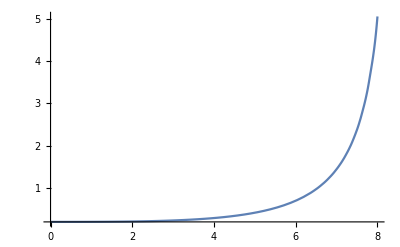

```mathematica
Plot[A11[t],{t,0,8},PlotRange->All]
```

```mathematica
(*Gauss Constraints*)
```

```mathematica
GC1[t_]= YMeq[[1]][[1]]/.{Subscript[A, a_,b_]'[t]->Subscript[P, a,b][t]};
```

```mathematica
GC2[t_]= YMeq[[2]][[1]]/.{Subscript[A, a_,b_]'[t]->Subscript[P, a,b][t]};
```

```mathematica
GC3[t_]= YMeq[[3]][[1]]/.{Subscript[A, a_,b_]'[t]->Subscript[P, a,b][t]};
```

```mathematica
GC11[t_]=-0.5 A11[t] P21[t]-0.5 A32[t] P22[t]+0.5 A21[t] P31[t]+0.5 A22[t] P32[t]-0.25 A71[t] P41[t]-0.25 A72[t] P42[t]+0.25 A61[t] P51[t]+0.25 A62[t] P52[t]-0.25 A51[t] P61[t]-0.25 A52[t] P62[t]+0.25 A41[t]P71[t]+0.25 A42[t] P72[t];
```

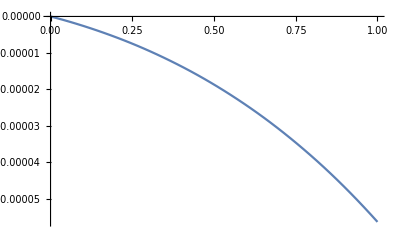

```mathematica
Plot[%173,{t,0,1},PlotRange->All]
```